```mathematica
17/155
```

```mathematica
Simplify[x(1-a)(1-b)+x a+x b(1-a)]
```

x

```mathematica
Simplify[(1-e)/2 (1-γ)(1-δ)+(1+e)/2+(1-e)/2 (1-γ)δ+(1-e)/2  γ]
```

1

```mathematica
(*meiotic division of W/H cells*)
homA=(1+eeA)/2;
θA=(1-γ)(1-eeA)/2;
γdashA=(1-eeA)γ/2;

homB=(1+eeB)/2;
θB=(1-γ)(1-eeB)/2;
γdashB=(1-eeB)γ/2;

(*ww,wa,aa,wr,rr,ar,wb*)

mw=(Mww+ θA Mwa+Mwr/2+ θB Mwb);
ma=(Maa+ homA Mwa+Mar/2+  Mab/2);
mb=(Mbb+ homB Mwb+Mbr/2+  Mab/2);
mr=(Mrr+ γdashA Mwa+Mwr/2+Mar/2+ γdashB Mwb+Mbr/2);

fw=(Fww+ ωA θA Fwa+Fwr/2+ωB θB Fwb);
fa=(ωA homA Fwa);
fb=( ωB homB Fwb);
fr=(ωA γdashA Fwa+Fwr/2+ωB  γdashB Fwb);

nFww=mw fw;
nFwa=mw fa+ma fw;
nFaa=ma fa;
nFwr=mw fr+mr fw;
nFrr=mr fr;
nFar=ma fr+mr fa;
nFwb=mw fb+mb fw;
nFab=ma fb+mb fa;
nFbb=mb fb;
nFbr=mb fr+mr fb;

nMww=mw fw;
nMwa=mw fa+ma fw;
nMaa=ma fa;
nMwr=mw fr+mr fw;
nMrr=mr fr;
nMar=ma fr+mr fa;
nMwb=mw fb+mb fw;
nMab=ma fb+mb fa;
nMbb=mb fb;
nMbr=mb fr+mr fb;

tot=Simplify[Total[{nFww,nFwa,nFaa,nFwr,nFrr,nFar,nFwb,nFab,nFbb,nFbr,nMww,nMwa,nMaa,nMwr,nMrr,nMar,nMwb,nMab,nMbb,nMbr}]];
next=Simplify[{nFww,nFwa,nFaa,nFwr,nFrr,nFar,nFwb,nFab,nFbb,nFbr,nMww,nMwa,nMaa,nMwr,nMrr,nMar,nMwb,nMab,nMbb,nMbr}/tot];
AppendTo[next,(Fwr+Fww+Fwa ωA+Fwb ωB)];
```

```mathematica
Runit[eeAb_,eeBb_,γB_,ωaB_,ωbB_,initial_,generations_,colours_,output_,label_]:=Block[{list,pars,lll,allelelist},
pars={eeA->eeAb,eeB->eeBb,γ->γB,ωA->ωaB,ωB->ωbB};
list=
NestList[next/.pars/.{Fww->#[[1]],Fwa->#[[2]],Faa->#[[3]],Fwr->#[[4]],Frr->#[[5]],Far->#[[6]],Fwb->#[[7]],Fab->#[[8]],Fbb->#[[9]],Fbr->#[[10]],Mww->#[[11]],Mwa->#[[12]],Maa->#[[13]],Mwr->#[[14]],Mrr->#[[15]],Mar->#[[16]],Mwb->#[[17]],Mab->#[[18]],Mbb->#[[19]],Mbr->#[[20]],tt->#[[21]]}&,initial,generations];
allelelist=Map[{
(Sum[#[[i]],{i,{1,11}}]+0.5 Sum[#[[i]],{i,{2,4,7,12,14,17}}])/Total[#[[1;;20]]],
(Sum[#[[i]],{i,{3,13}}]+0.5 Sum[#[[i]],{i,{2,6,8,12,16,18}}])/Total[#[[1;;20]]],
(Sum[#[[i]],{i,{9,19}}]+0.5 Sum[#[[i]],{i,{7,8,10,17,18,20}}])/Total[#[[1;;20]]],
(Sum[#[[i]],{i,{5,15}}]+0.5 Sum[#[[i]],{i,{4,6,10,14,16,20}}])/Total[#[[1;;20]]],#[[21]]}&,list];
Which[
output=="table",MatrixForm[list],
output=="list",list,
output=="allele",Legended[ListLinePlot[Table[Transpose[{Range[0,generations],allelelist[[All,ii]]}],{ii,Length[allelelist[[1]]]}],PlotStyle->colours,Frame->True,PlotRange->{{0,generations},{0,1.05}},FrameLabel->{"Generation","Frequency"},FrameStyle->Black,PlotLabel->label],Placed[LineLegend[colours,{"W","A","B","R","Pop. fitness"},LegendFunction->"Frame",LegendLayout->{"Row",2}],Below]],
output=="alleleNoLeg",ListLinePlot[Table[Transpose[{Range[0,generations],allelelist[[All,ii]]}],{ii,Length[allelelist[[1]]]}],PlotStyle->colours,Frame->True,PlotRange->{{0,generations},{0,1.05}},FrameLabel->{"Generation","Frequency"},FrameStyle->Black,PlotLabel->label],
output=="allelelist",MatrixForm[allelelist]]];
```

2

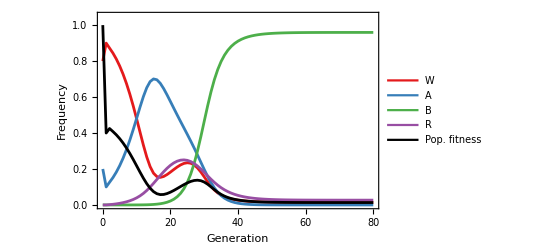

2

```mathematica
(*Set up the initial conditions*)
initial=ConstantArray[0,22];
initial[[21]]=1;
initial[[1]]=initial[[11]]=(1-initA-initB)/2;
initial[[3]]=initial[[13]]=initA/2;
initial[[9]]=initial[[19]]=initB/2;
Simplify[Total[initial]]
(*-----------------------------*)
colours={RGBColor[Rational[76, 85], Rational[26, 255], Rational[28, 255]],RGBColor[Rational[11, 51], Rational[42, 85], Rational[184, 255]],RGBColor[Rational[77, 255], Rational[35, 51], Rational[74, 255]],RGBColor[Rational[152, 255], Rational[26, 85], Rational[163, 255]],Black};
Runit[eeAb=0.95,eeBb=0.95,γB=0.5,ωaB=0.25,ωbB=.95,initial/.{initA->0.2,initB->0.000001},generations=80,colours,"allele",""]
```